Requires to Run HeatConduction_2D.nb

# Core Routines

## Return the Heat Conduction Variables

```mathematica
(*Given full set of variables, the following routine returns the variables involved in heat conduction.
These are those variables which have only an x-index. Since they are the ones which are involved in the heat conduction.*)
ReturnHeatVar[var_]:=Module[{result,pos},
result={};
pos={};

(*The assumption is that none of the variables contain the z-index. Therefore we only check for the y index. If the y index is zero then the variabls is involved in heat conduction*)
Do[If[var⟦ii⟧⟦3⟧==0,result=Join[result,{var⟦ii⟧}];pos=Join[pos,{{ii}}];];
,{ii,1,Length[var]}];

(*we also return the total number of variables involved in the heat conduction. The final result includes at first the variables involved in heat conduction and then the variables which were left out.*)
{Join[result,Delete[var,pos]],Length[pos]}
]
```

## Return the Matrix for Heat Conduction

```mathematica
MatrixHeat[Mat_,var_,varHeat_,numHeat_]:=Module[{Permute,PermuteInv,MatHeat},

(*Permute the variables such that the variables for Heat conduction appear first.*)
Permute=PermuteVar[var,varHeat];
PermuteInv=PermuteVar[varHeat,var];

(*Matrix such that the Heat Conduction matrix appears as the upper block*)
MatHeat=PermuteInv.Mat.Permute;

(*we first extract the matrix which plays a role in heat conduction*)
MatHeat=MatHeat⟦1;;numHeat,1;;numHeat⟧;

(*we now remove the rows corresponding to normal velocity and density. That means the upper block of 2 X 2 size*)
MatHeat=MatHeat⟦3;;-1,3;;-1⟧;

MatHeat
]
```

## Solving Routine(Core)

```mathematica
Clear[res,nn,var,eqn,b0,A0,P0,a,n,w,ww,unknowns,λ0,λ,λPlus,vv,v,Ansatz,Coefs,v0,v1,v2,v3,v4,C0,k,x]
```

```mathematica
GetSolutionHeat[Ntensors_]:=Block[{res,nn,var,varC,eqn,b0,a,n,w,dw,λ0,λ,λPlus,v,vv,Ansatz,Coefs,C0,Signum,SymmetryConditions,k,x,jj,ii,Kn,α,numEqn},


(*Delete is for removing the density and the velocity. The reason for removing the first equation is obvious. aIdx[[1]]+1 removes the energy balance because it contains the denstiy and the stress tensor. Since we are not interested in density, we let it go.*)

SystemData=FinalMatrices[Ntensors];
A0=MatrixHeat[SystemData⟦1⟧,SystemData⟦5⟧,ReturnHeatVar[SystemData⟦5⟧]⟦1⟧,ReturnHeatVar[SystemData⟦5⟧]⟦2⟧];
numEqn=Length[A0];

P0=SparseArray[{{i_,i_}->-1},numEqn];

(*only for energy balance, the momentum equation and the mass conservation has been ignored. *)
P0⟦1,1⟧=0;

(*generalized eigen vector and eigen value of P0 with respect to A0*)
{λ0,vv}=Chop[Eigensystem[{P0,1.0A0}]];

(*remove the zero and the infinite eigen values, why do the infinite eigen values appear? *)
λ=Select[λ0,(0<Abs[#]<∞)&];
v=Extract[vv,Flatten[Table[Position[λ0,item],{item,Select[λ0,(0<Abs[#]<∞)&]}],1]];

(*assumes symmetric spectrum*)
λ=Flatten[Table[{Rationalize[λ⟦ii⟧,0],-Rationalize[λ⟦ii⟧,0]},{ii,1,Length[λ],2}]];


λPlus=Select[λ,(#>0)&];

(*a polynomial ansatz*)
Ansatz[x_]=Table[Sum[coef[jj,ii] x^jj,{jj,0,4}],{ii,1,numEqn}];
Coefs=Flatten[Table[Table[coef[jj,ii],{jj,0,4}],{ii,1,numEqn}]];

(*vector for the forcing term*)
B0=Table[0,{i,1,numEqn}];
B0⟦1⟧=1;

(*ansatz for the particular solution of the equations.*)
Ansatz[x_]=Ansatz[x]/.Solve[Thread[Flatten[CoefficientList[A0.Ansatz'[x]-1/Kn P0.Ansatz[x]+α B0 x^2,x]]==0],Coefs]⟦1⟧/.{coef[_,_]->0};

Signum=Table[0,{ii,1,Length[λ],2}];

(*store the sign of the first non-zero entry in the eigenvectors*)

Do[jj=1;While[v⟦ii,jj⟧==0,jj++];Signum⟦(ii+1)/2⟧=-Sign[v⟦ii+1,jj⟧/v⟦ii,jj⟧],{ii,1,Length[λ],2}];
SymmetryConditions=Table[k[ii]->-Signum⟦(ii+1)/2⟧k[ii+1],{ii,1,Length[λ],2}];

(*The final result is the particular solution + the solution to the homogeneous problem. The particular solution is the Ansatz and the homogeneous solution is the part: C0 B0+Sum[k[ii] v⟦ii⟧Exp[λ⟦ii⟧x/Kn]*)

res=Chop[ExpToTrig[C0 B0+Ansatz[x]+Sum[k[ii] v⟦ii⟧Exp[λ⟦ii⟧x/Kn],{ii,1,Length[λ]}]/.SymmetryConditions/.Table[k[ii]->k[ii/2],{ii,1,Length[λ]}]]]/.Table[k[ii]->k[ii]Exp[-λPlus⟦ii⟧(1/2)/Kn],{ii,1,Length[λPlus]}]

];
```

```mathematica
u[x_]=GetSolutionHeat[11];

Chop[Expand[N[A0.u'[x]-1/Kn P0.u[x]+α B0 x^2]]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{0,0,0,0,0,0,0,0,0}

## Boundary Conditions

```mathematica
GetBoundaryHeat[B_,var_,varOdd_]:=Module[{result,PermuteMat,varHeat,Bheat,PermuteMatOdd,varHeatOdd,numVarHeat,numVarHeatOdd,Brhs},


{varHeat,numVarHeat}=ReturnHeatVar[var];
{varHeatOdd,numVarHeatOdd}=ReturnHeatVar[var⟦varOdd⟧];

PermuteMat=PermuteVar[var,varHeat];
PermuteMatOdd=PermuteVar[varHeatOdd,var⟦varOdd⟧];

(*Ignoring the boundary condition from vx and the contribution from ρ and vx. Originally the boundary conditions are of the form Bu = g. Where u contains all the variables. So we first multiply from the left by the permutation matrix so that we collect the odd variables of the heat conduction problem. Then we multiply from the right so that we collect at the variables for the heat conduction problem. *)
Bheat=FullSimplify[PermuteMatOdd.B.PermuteMat]⟦2;;numVarHeatOdd,3;;numVarHeat⟧;
Brhs=-√(3/2)Bheat⟦All,1⟧θW;
(*We return the boundary in the form B.u+g*)
Bheat.varHeat⟦3;;numVarHeat⟧-Brhs
]
GetBoundaryHeat2[B_,var_,varOdd_]:=Module[{result,PermuteMat,varHeat,Bheat,PermuteMatOdd,varHeatOdd,numVarHeat,numVarHeatOdd,Brhs},

{varHeat,numVarHeat}=ReturnHeatVar[var];
{varHeatOdd,numVarHeatOdd}=ReturnHeatVar[var⟦varOdd⟧];

PermuteMat=PermuteVar[var,varHeat];
PermuteMatOdd=PermuteVar[varHeatOdd,var⟦varOdd⟧];

(*Ignoring the boundary condition from vx and the contribution from ρ and vx*)
Bheat=FullSimplify[PermuteMatOdd.B.PermuteMat];
Brhs=-√(3/2)Bheat⟦All,1⟧θW;
(*We return the boundary in the form B.u+g*)
Bheat
]
```

## Solving Procedure

```mathematica
(*flag == 0 for OBC and flag == 1 for MBC*)
GetHeatConduction[kn_,θw_,alpha_,Ntensors_,flag_]:=Module[{varHeat,numVarHeat,U,BC,BCrhs,BCmatrix,bcSol},

U=GetSolutionHeat[Ntensors];

(*we first collect all the variables*)
(*The value of SystemData is prescribed inside the GetSolutionHeat*)
{varHeat,numVarHeat}=ReturnHeatVar[SystemData⟦5⟧];

(*we now remove density and velocity from the set of variables*)
varHeat=varHeat⟦3;;numVarHeat⟧;

Which[flag==0,
BC=GetBoundaryHeat[SystemData⟦3⟧,SystemData⟦5⟧,SystemData⟦6⟧];,
flag == 1,
BC=GetBoundaryHeat[SystemData⟦4⟧,SystemData⟦5⟧,SystemData⟦6⟧];
];


{BCrhs,BCmatrix}=CoefficientArrays[(BC/.Table[varHeat⟦ii⟧->U⟦ii⟧/.{x->1/2},{ii,1,Length[varHeat]}]/.{χ1->1,Kn->kn}),Join[{C0},Table[k[ii],{ii,1,Length[BC]-1}]]];

bcSol=Thread[Join[{C0},Table[k[ii],{ii,1,Length[BC]-1}]]->Chop[-Inverse[BCmatrix].BCrhs]];


{-√(2/3),√2,-√(5/2)}Expand[U/.bcSol/.{Kn->kn,θW->θw,α->alpha}]⟦{1,2,3}⟧
]
```

# Reference Solution

```mathematica
exactKn0p1 = Import["refs/Archive/BGKPoiseuilleHeat/Result_BGKreduced_tau0p1_nst600_Nc300_cMax5p0.dat"];

exactKn0p3 = Import["refs/Archive/BGKPoiseuilleHeat/Result_BGKreduced_tau0p3_nst600_Nc300_cMax5p0.dat"];

exactKn0p5 = Import["refs/Archive/BGKPoiseuilleHeat/Result_BGKreduced_tau0p5_nst600_Nc300_cMax5p0.dat"];

(*fix for the wall temperature*)
exactKn0p1⟦All,4⟧+=1;
exactKn0p3⟦All,4⟧+=1;
exactKn0p5⟦All,4⟧+=1;

θExactKn0p1=Interpolation[exactKn0p1⟦All,{1,4}⟧];
σExactKn0p1 = Interpolation[exactKn0p1⟦All,{1,6}⟧];
qExactKn0p1 = Interpolation[exactKn0p1⟦All,{1,7}⟧];

θExactKn0p3=Interpolation[exactKn0p3⟦All,{1,4}⟧];
σExactKn0p3 = Interpolation[exactKn0p3⟦All,{1,6}⟧];
qExactKn0p3 = Interpolation[exactKn0p3⟦All,{1,7}⟧];

θExactKn0p5=Interpolation[exactKn0p5⟦All,{1,4}⟧];
σExactKn0p5 = Interpolation[exactKn0p5⟦All,{1,6}⟧];
qExactKn0p5 = Interpolation[exactKn0p5⟦All,{1,7}⟧];
```

```mathematica
θExactKn0p3[x]
```

InterpolatingFunction[{{-0.5, 0.5}}, <>][x]

# Results (source independent of Kn)

### Plotting routine

```mathematica
PlotsPaper:=Module[{plotLegends,fontsize,fontsize2},

plotLegends={"MBC","OBC","Reference"};
fontsize = 14;
fontsize2 = 16;

(*we consider a y as the axes label to main consistency with Manuels paper*)
{Plot[{1/3(temperatureFullKn0p3MBC[16][x]+temperatureFullKn0p3MBC[20][x]+temperatureFullKn0p3MBC[12][x]),1/3(temperatureFullKn0p3OBC[16][x]+temperatureFullKn0p3OBC[20][x]+temperatureFullKn0p3OBC[12][x]),θExactKn0p3[x]},{x,0,0.5},PlotLegends->plotLegends,PlotStyle->{{Thick,colorlist⟦2⟧},{Thick,colorlist⟦3⟧},{Thick,Black}},GridLines->Automatic,Frame->True,Axes->True,FrameTicksStyle->Directive[FontSize->fontsize],FrameLabel->{{Style["θ̃",FontSize->fontsize2],None},{Style["x",FontSize->fontsize2],None}},ImageSize->600,RotateLabel->False],Plot[{1/3(stressFullKn0p3MBC[16][x]+stressFullKn0p3MBC[20][x]+stressFullKn0p3MBC[12][x]),1/3(stressFullKn0p3OBC[16][x]+stressFullKn0p3OBC[20][x]+stressFullKn0p3OBC[12][x]),σExactKn0p3[x]},{x,0,0.5},PlotLegends->plotLegends,PlotStyle->{{Thick,colorlist⟦2⟧},{Thick,colorlist⟦3⟧},{Thick,Black}},GridLines->Automatic,Frame->True,Axes->True,FrameTicksStyle->Directive[FontSize->fontsize],FrameLabel->{{Style["(σ̃)_yy",FontSize->fontsize2],None},{Style["x",FontSize->fontsize2],None}},ImageSize->600,RotateLabel->False]}
]

ErrorPlotsPaper:=Module[{plotLegends,fontsize,fontsize2},

plotLegends={"MBC","OBC"};
fontsize = 14;
fontsize2 = 16;

(*we consider a y as the axes label so as to maintain consistency*)
{Plot[{Abs[1/3(temperatureFullKn0p3MBC[16][x]+temperatureFullKn0p3MBC[20][x]+temperatureFullKn0p3MBC[12][x])-θExactKn0p3[x]],Abs[1/3(temperatureFullKn0p3OBC[16][x]+temperatureFullKn0p3OBC[20][x]+temperatureFullKn0p3OBC[12][x])-θExactKn0p3[x]]},{x,0,0.5},PlotLegends->plotLegends,PlotStyle->{{Thick,colorlist⟦2⟧},{Thick,colorlist⟦3⟧},{Thick,Black}},GridLines->Automatic,Frame->True,Axes->True,FrameTicksStyle->Directive[FontSize->fontsize],FrameLabel->{{Style["Error(θ̃)",FontSize->fontsize2],None},{Style["y",FontSize->fontsize2],None}},ImageSize->600,RotateLabel->False],Plot[{Abs[1/3(stressFullKn0p3MBC[16][x]+stressFullKn0p3MBC[20][x]+stressFullKn0p3MBC[12][x])-σExactKn0p3[x]],Abs[1/3(stressFullKn0p3OBC[16][x]+stressFullKn0p3OBC[20][x]+stressFullKn0p3OBC[12][x])-σExactKn0p3[x]]},{x,0,0.5},PlotLegends->plotLegends,PlotStyle->{{Thick,colorlist⟦2⟧},{Thick,colorlist⟦3⟧},{Thick,Black}},GridLines->Automatic,Frame->True,Axes->True,FrameTicksStyle->Directive[FontSize->fontsize],FrameLabel->{{Style["Error(OverTilde[σ_yy])",FontSize->fontsize2],None},{Style["y",FontSize->fontsize2],None}},ImageSize->600,RotateLabel->False]}
]
```

### Full

#### Kn 0.1

```mathematica
Kn = 0.1;
θW=1.0;
α=√(2/3);

Do[Print[Style["Num Tensors: ",FontColor->Magenta],ii];
{temperatureFullKn0p1[ii][x_],stressFullKn0p1[ii][x_],heatFullKn0p1[ii][x_]}=GetHeatConduction[Kn,θW,α,ii,0];,{ii,NtensorsFullTheories⟦1;;-2⟧}];
```

Num Tensors: 6

Num Tensors: 9

Num Tensors: 12

Num Tensors: 16

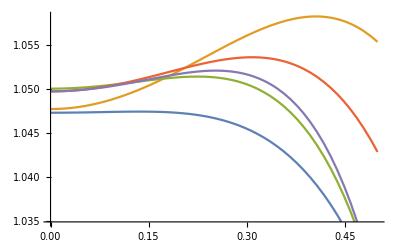

```mathematica
plots=Table[temperatureFullKn0p1[ii][x],{ii,NtensorsFullTheories}];
Plot[plots,{x,0,0.5},PlotLegends->NamesFullTheries]
```

```mathematica
errorFullTheories =Table[ NIntegrate[Abs[ii-θExactKn0p1[x]],{x,-0.5,0.5}],{ii,plots}];
errorFullTheories=Table[Flatten[{NtensorsFullTheories⟦ii⟧,errorFullTheories⟦ii⟧}],{ii,Length[errorFullTheories]}];
```

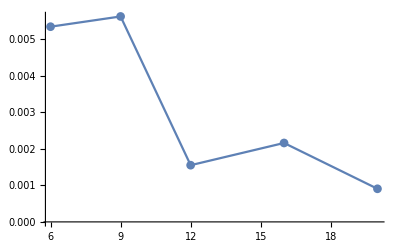

```mathematica
ListPlot[errorFullTheories,Joined->True,PlotMarkers->Automatic]
```

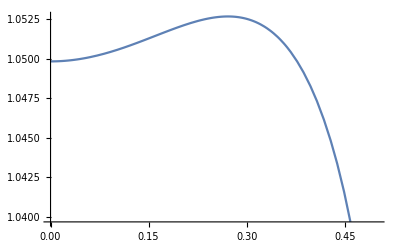

```mathematica
Plot[θExactKn0p1[x],{x,0,0.5},PlotLegends->Automatic]
```